## Module - vary Ls and Lv

Here we keep constant the sum of the arm of the hinged counter weight plus the arm from the pivot to the arm of the counterweight. The long arm varies length. To take into account the increasing mass of the arm we assume that the linear density is kept constant and that we can multiply it by the given lenfth of the long arm.

```mathematica
ClearAll["Global`*"]
```

#### Initial Conditions

#### Mod

```mathematica
v45[cwL_,longL_]:=
Module[{Lcw=cwL,Lb=longL,theta0,phi0,thetashot,Mp,Mcw ,Mb,Mbase,Msy,g,Lt,V,theta,t,phi,xp,yp,xcw,ycw,Ib,xpd,ypd,xcwd,ycwd,T,L,sol,x,tmax,thetaDer,xder,vxpro,vypro,xpos,ypos,thetat,tshot,vshot,EL,linMass,Ls},

EL[q_]:=D[L,q[t]]-D[D[L,q'[t]],t]==0;

theta0 = 0.849;
phi0 = 0;
thetashot=-Pi/4;
Mp = 0.002;
Mcw = 0.162;
Mbase = 0.485;
Msy = Mbase+Mb+Mcw+Mp;
g =9.81;
Lt=  .415 ;
Ls= Lt - Lcw;
linMass=0.0422;
Mb = linMass*(Lb+Ls);

V= -Mp*Lb* Sin[theta[t]]*g + (Ls*Sin[theta[t]]-Lcw*Cos[phi[t]])*g*Mcw - 1/2 *Sin[theta[t]]*Mb*g*(Lb-Ls);

xp =- Lb *Cos[theta[t]]+x[t];
yp = - Lb*Sin[theta[t]];
xcw = Ls *Cos[theta[t]]+x[t]+Lcw *Sin[phi[t]];
ycw = Ls *Sin[theta[t] ]-Lcw *Cos[phi[t]];
Ib =Mb*1/3 ((Lb^3+Ls^3)/(Lb+Ls));
xpd=D[xp,t];
ypd=D[yp,t];
xcwd=D[xcw,t];
ycwd=D[ycw,t];
T=1/2*Mp* (xpd^2+ypd^2)+1/2 *Mcw*(xcwd^2+ycwd^2)+Msy*1/2*x'[t]^2+1/2 *Ib*theta'[t]^2;

L = T-V;

sol = First[NDSolve[{EL[theta],EL[phi],EL[x],
x[0]==0,
theta[0]==theta0,
phi[0]== phi0,
x'[0]==0,
theta'[0]==0,
phi'[0]==0},{x,theta,phi},{t,0,tmax=10}]];

thetaDer[t_]=D[theta[t]/.sol,t];
xder[t_]=D[x[t]/.sol,t];
vxpro[t_] :=Lb *Sin[theta[t]/.sol]*thetaDer[t]+xder[t];
vypro[t_]:=-Lb*Cos[theta[t]/.sol]*thetaDer[t];
xpos[t_] :=-Lb Cos[theta[t]/.sol]+x[t]/.sol;
ypos[t_]:=-Lb Sin[theta[t]/.sol];
thetat[t_]:= theta[t]/.sol;
tshot=Solve[thetat[t]== thetashot,t][[1,1,2]];

vshot=Sqrt[vxpro[tshot]^2+vypro[tshot]^2]
]
```

```mathematica
smin=0.075;
smax=0.2;
lmin=0.2;
lmax=0.7;
```

Here we create a table of values of varying lengths. This takes a long time to run and small changes on the time step produce very different results.

```mathematica
vDat=Monitor[Table[{s,l,v45[s,l]},{s,smin,smax,0.001},{l,lmin,lmax,0.02}],s]
```

```mathematica
Flatten[vDat,1][[1479]]
```

{0.131,0.7,8.10613}

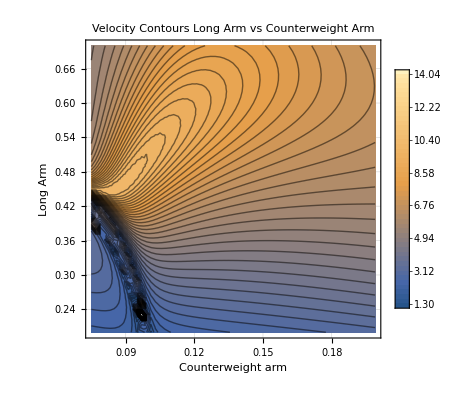

```mathematica
ListContourPlot[Flatten[vDat,1],Contours->50,GridLines->Automatic, PlotLabel->"Velocity Contours Long Arm vs  Counterweight Arm", FrameLabel->{"Counterweight arm","Long Arm"},PlotLegends->Automatic,Contours->70]
```